```mathematica
(*dimensions*)
	l=16;
	m=4;
	Nb=l m;
(* IVLCB S-BOX *)

sbox="0FE5D36CB9A87421";
cx=IntegerDigits[FromDigits[sbox,16],16,16]
S[x_]:=cx[[x+1]]
```

{0,15,14,5,13,3,6,12,11,9,10,8,7,4,2,1}

```mathematica
delta=1
Table[{i,i2=BitXor[i,delta],S[i],S[i2],BitXor[S[i],S[i2]]},{i,0,15}];
```

1

```mathematica
ClearAll[DTT]
DTT[delta_]:=
(
diffs=Table[(i2=BitXor[i,delta];BitXor[S[i],S[i2]]),{i,0,15}];
weights=Map[{#,Count[diffs,#]}&,Range[0,15]]
)
DTT[]:=DTT[]=Map[Last,Map[DTT,Range[0,15]],{2}]
```

```mathematica
DTTSparse[delta_,threshold_]:=Module[
{},
weights=DTT[delta];
Map[{delta,#[[1]],#[[2]]}&,Select[weights,#[[2]]>=threshold&]]
]
```

```mathematica
G4
```

{{{0,0,16}},{{1,2,4},{1,3,4}},{{2,1,4},{2,5,4}},{{3,1,4},{3,3,4},{3,5,4},{3,6,4}},{{4,8,4},{4,9,4},{4,12,4},{4,13,4}},{{5,2,4},{5,3,4}},{{6,3,4},{6,6,4}},{},{{8,4,4},{8,13,4}},{{9,4,4},{9,9,4}},{},{},{{12,4,4},{12,12,4}},{{13,4,4},{13,8,4}},{},{}}

```mathematica
G4=Flatten[Map[DTTSparse[#,4]&,Range[0,15]],1];
H4=Graph[Map[DirectedEdge@@#&,G4],DirectedEdges->True]
```

-Graphics-

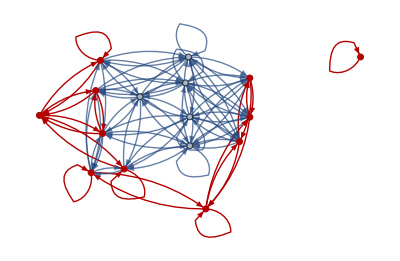

```mathematica
G2=Flatten[Map[DTTSparse[#,2]&,Range[0,15]],1];
H2=Graph[Map[DirectedEdge@@#&,G2],DirectedEdges->True];
HighlightGraph[Graph@H2,Graph@H4]
```

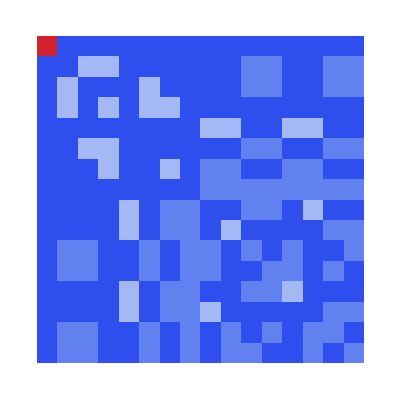

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 4 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 4 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 4 | 4 | 0 | 0
0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 2
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 2
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 4 | 0 | 0 | 0 | 0 | 0 | 2 | 2
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 0
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 2)

```mathematica
S2=SparseArray@Map[{#[[1]],#[[2]]}+1->#[[3]]&,G2];

ArrayPlot[S2,ColorFunction->"TemperatureMap"]
Normal@S2//MatrixForm
```

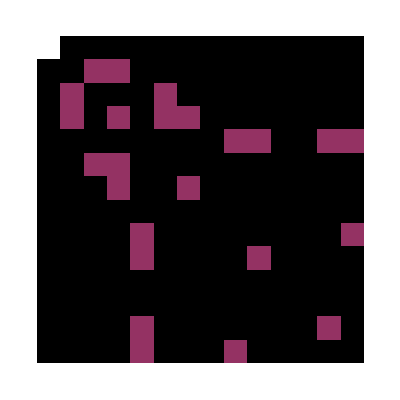

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 4 | 4
0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0)

```mathematica
S4=SparseArray@Map[{#[[1]],#[[2]]}+1->#[[3]]&,G4];

ArrayPlot[S4,ColorFunction->"SunsetColors"]
Normal@S4//MatrixForm
```

```mathematica
G4
```

{{0,0,16},{1,2,4},{1,3,4},{2,1,4},{2,5,4},{3,1,4},{3,3,4},{3,5,4},{3,6,4},{4,8,4},{4,9,4},{4,12,4},{4,13,4},{5,2,4},{5,3,4},{6,3,4},{6,6,4},{8,4,4},{8,13,4},{9,4,4},{9,9,4},{12,4,4},{12,12,4},{13,4,4},{13,8,4}}

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 4 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 4 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 4 | 4 | 0 | 0
0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2
0 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 2
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 2
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 4 | 0 | 0 | 0 | 0 | 0 | 2 | 2
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 0
0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 2)

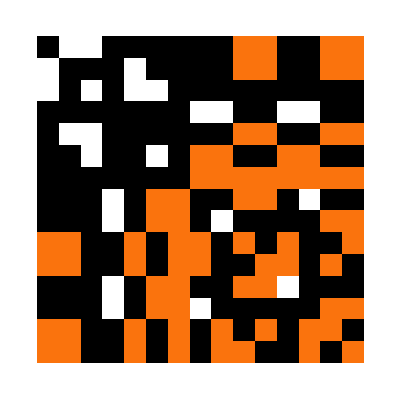

```mathematica
DTT[]//MatrixForm
Transpose[Drop[Transpose[Drop[DTT[],1]],1]]//ArrayPlot[#,ColorFunction->"SunsetColors"]&
```

```mathematica
pi={31 ,6 ,29, 14, 1, 12, 21, 8, 27, 2, 3, 0, 25, 4, 23, 10}
```

{31,6,29,14,1,12,21,8,27,2,3,0,25,4,23,10}

```mathematica
Length[pi]
```

16

linear  characteristics

```mathematica
{a,b}
```

s

```mathematica
LAT[alpha_,beta_]:=Count[Table[Mod[DigitCount[BitAnd[alpha,x],2,1]+DigitCount[BitAnd[beta,S[x]],2,1],2],{x,0,2^m-1}],0]
```

```mathematica
LAT[alpha_]:=Table[{beta,LAT[alpha,beta]},{beta,0,2^m-1}]
```

```mathematica
LAT[2]
```

{{0,8},{1,4},{2,8},{3,12},{4,8},{5,8},{6,8},{7,8},{8,8},{9,12},{10,8},{11,12},{12,8},{13,8},{14,8},{15,8}}

```mathematica
LAT[]:=LAT[]=Table[LAT[alpha,beta],{alpha,0,2^m-1},{beta,0,2^m-1}]
```

```mathematica
LAT[]//TableForm
bias=Abs[LAT[]-8]/16;bias//TableForm
ArrayPlot[bias,ColorFunction->"LightTemperatureMap"]
```

```mathematica
LATSparse[alpha_,threshold_]:=Module[
{},
weights=LAT[alpha];
Map[{alpha,#[[1]],Abs[(#[[2]]-8)/16]}&,Select[weights,Abs[(#[[2]]-8)/16]>=threshold&]]
]
```

```mathematica
Manipulate[
G4=Flatten[Map[LATSparse[#,t]&,Range[0,2^m-1]],1];
H4=Graph[Map[DirectedEdge@@#&,G4],DirectedEdges->True],{t,0,1/2,0.001}]
```

Part::partw: Part 17 of {0,15,14,5,13,3,6,12,11,9,«6»} does not exist.

Part::partw: Part 18 of {0,15,14,5,13,3,6,12,11,9,«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
DDTSparse[3,2]
LATSparse[3,2]
```

DDTSparse[3,2]

{{3,0,8},{3,1,6},{3,2,12},{3,3,10},{3,4,8},{3,5,10},{3,6,8},{3,7,10},{3,8,8},{3,9,6},{3,10,8},{3,11,6},{3,12,8},{3,13,10},{3,14,12},{3,15,6}}

```mathematica
P
```